```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]]
```

/Users/ethanspangler/StabilityProject

```mathematica
"/Users/ethanspangler/StabilityProject"
```

/Users/ethanspangler/StabilityProject

Plots of Freedonia, Merika, and Kleptopia for low initial dissent.

```mathematica
Freedonia =Import["dataFreedonia.mx"] // Dataset;
Merika =Import["dataMerika.mx"] // Dataset;
Kleptopia=Import["dataKleptopia.mx"]//Dataset;
Cathay=Import["dataCathay.mx"]//Dataset;
Rentistan=Import["dataRentistan.mx"]//Dataset;
Develpolus=Import["dataDevelpolus.mx"]//Dataset;
Bellicostia=Import["dataBellicostia.mx"]//Dataset;
Hippieberg=Import["dataHippieberg.mx"]//Dataset;
```

New lines to convert Scientific form to plotable form:

```mathematica
Freedonia = Freedonia/.ScientificForm[n_,rest___]->n;
Merika = Merika/.ScientificForm[n_,rest___]->n;
Kleptopia = Kleptopia/.ScientificForm[n_,rest___]->n;
Cathay= Cathay/.ScientificForm[n_,rest___]->n;
Rentistan= Rentistan/.ScientificForm[n_,rest___]->n;
Develpolus= Develpolus/.ScientificForm[n_,rest___]->n;
Bellicostia= Bellicostia/.ScientificForm[n_,rest___]->n;
Hippieberg= Hippieberg/.ScientificForm[n_,rest___]->n;
```

The plots are a little two close together. I’m going to have to break them up for clarity. I’m thinking 3 different plots.

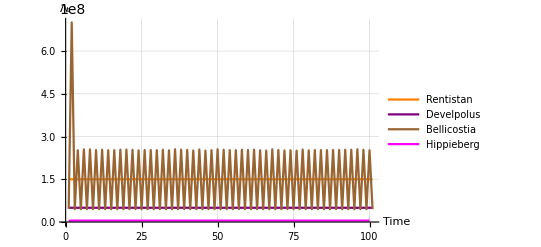

```mathematica
ListLinePlot[{(*Freedonia[All,3]//Normal,Merika[All,3]//Normal,
Cathay[All,3]//Normal,*)
Rentistan[All,3]//Normal,
Develpolus[All,3] //Normal,
Bellicostia[All,3]//Normal,
Hippieberg[All,3]//Normal},PlotLegends->{(*"Freedonia","Merika","Cathay",*)"Rentistan","Develpolus","Bellicostia","Hippieberg"},PlotStyle->{(*Green,Blue,Pink,*)Orange,Purple,Brown, Magenta},GridLines->Automatic,
(*PlotLabel->Style["Stability with low initial dissent", FontSize->12],*)
PlotRange->Full,AxesLabel->{"Time","Λ_t"}]
```

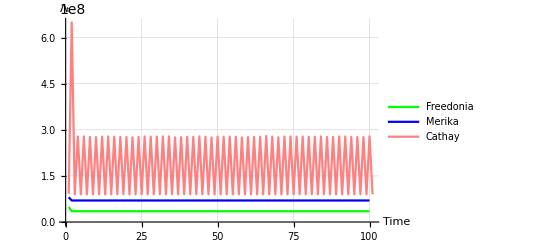

```mathematica
ListLinePlot[{Freedonia[All,3]//Normal,Merika[All,3]//Normal,
Cathay[All,3]//Normal(*,
Rentistan[All,3]//Normal,
Develpolus[All,3] //Normal,
Bellicostia[All,3]//Normal,
Hippieberg[All,3]//Normal*)},PlotLegends->{"Freedonia","Merika","Cathay"(*,"Rentistan","Develpolus","Bellicostia","Hippieberg"*)},PlotStyle->{Green,Blue,Pink(*,Orange,Purple,Magenta,Brown*)},GridLines->Automatic,
(*PlotLabel->Style["Stability with low initial dissent", FontSize->12],*)
PlotRange->Full,AxesLabel->{"Time","Λ_t"}]
```

The last plot, just Kleptopia

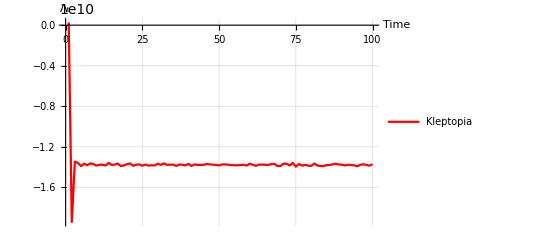

```mathematica
ListLinePlot[{Kleptopia[All,3]//Normal },PlotLegends->{"Kleptopia"},PlotStyle->{Red},GridLines->Automatic,
(*PlotLabel->Style["Stability with low initial dissent", FontSize->12],*)
PlotRange->Full,AxesLabel->{"Time","Λ_t"}]
```

Initial Plotting with a R shock,

```mathematica
FreedoniaRSHOCK =Import["dataFreedoniaRSHOCK.mx"] // Dataset;
MerikaRSHOCK =Import["dataMerikaRSHOCK.mx"] // Dataset;
KleptopiaRSHOCK=Import["dataKleptopiaRSHOCK.mx"]//Dataset;
CathayRSHOCK=Import["dataCathayRSHOCK.mx"]//Dataset;
RentistanRSHOCK=Import["dataRentistanRSHOCK.mx"]//Dataset;
DevelpolusRSHOCK=Import["dataDevelpolusRSHOCK.mx"]//Dataset;
BellicostiaRSHOCK=Import["dataBellicostiaRSHOCK.mx"]//Dataset;
HippiebergRSHOCK=Import["dataHippiebergRSHOCK.mx"]//Dataset;
```

```mathematica
FreedoniaRSHOCK = FreedoniaRSHOCK/.ScientificForm[n_,rest___]->n
MerikaRSHOCK = MerikaRSHOCK/.ScientificForm[n_,rest___]->n
KleptopiaRSHOCK = KleptopiaRSHOCK/.ScientificForm[n_,rest___]->n
CathayRSHOCK= CathayRSHOCK/.ScientificForm[n_,rest___]->n
RentistanRSHOCK= RentistanRSHOCK/.ScientificForm[n_,rest___]->n
DevelpolusRSHOCK= DevelpolusRSHOCK/.ScientificForm[n_,rest___]->n
BellicostiaRSHOCK= BellicostiaRSHOCK/.ScientificForm[n_,rest___]->n
HippiebergRSHOCK= HippiebergRSHOCK/.ScientificForm[n_,rest___]->n
```

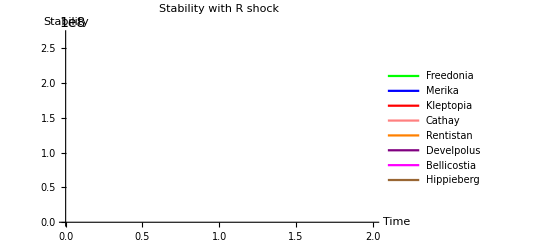

```mathematica
ListLinePlot[{FreedoniaRSHOCK[All,3]//Normal,MerikaRSHOCK[All,3]//Normal,KleptopiaRSHOCK[All,3] //Normal ,
CathayRSHOCK[All,3]//Normal,
RentistanRSHOCK[All,3]//Normal,
DevelpolusRSHOCK[All,3] //Normal,
BellicostiaRSHOCK[All,3]//Normal,
HippiebergRSHOCK[All,3]//Normal},PlotLegends->{"Freedonia","Merika","Kleptopia","Cathay","Rentistan","Develpolus","Bellicostia","Hippieberg"},PlotStyle->{Green,Blue,Red,Pink,Orange,Purple,Magenta,Brown},
PlotLabel->Style["Stability with R shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"}]
```

ϕ shock plotting,

```mathematica
FreedoniaϕSHOCK =Import["dataFreedonia.mx"] // Dataset;
MerikaϕSHOCK =Import["dataMerikaϕSHOCK.mx"] // Dataset;
KleptopiaϕSHOCK=Import["dataKleptopiaϕSHOCK.mx"]//Dataset;
CathayϕSHOCK=Import["dataCathayϕSHOCK.mx"]//Dataset;
RentistanϕSHOCK=Import["dataRentistanϕSHOCK.mx"]//Dataset;
DevelpolusϕSHOCK=Import["dataDevelpolusϕSHOCK.mx"]//Dataset;
BellicostiaϕSHOCK=Import["dataBellicostiaϕSHOCK.mx"]//Dataset;
HippiebergϕSHOCK=Import["dataHippiebergϕSHOCK.mx"]//Dataset;
```

```mathematica
FreedoniaϕSHOCK = FreedoniaϕSHOCK/.ScientificForm[n_,rest___]->n;
MerikaϕSHOCK = MerikaϕSHOCK/.ScientificForm[n_,rest___]->n;
KleptopiaϕSHOCK = KleptopiaϕSHOCK/.ScientificForm[n_,rest___]->n;
CathayϕSHOCK= CathayϕSHOCK/.ScientificForm[n_,rest___]->n;
RentistanϕSHOCK= RentistanϕSHOCK/.ScientificForm[n_,rest___]->n;
DevelpolusϕSHOCK= DevelpolusϕSHOCK/.ScientificForm[n_,rest___]->n;
BellicostiaϕSHOCK= BellicostiaϕSHOCK/.ScientificForm[n_,rest___]->n;
HippiebergϕSHOCK= HippiebergϕSHOCK/.ScientificForm[n_,rest___]->n;
```

```mathematica
ListLinePlot[{FreedoniaϕSHOCK[All,3]//Normal,
MerikaϕSHOCK[All,3]//Normal,
KleptopiaϕSHOCK[All,3] //Normal ,
CathayϕSHOCK[All,3]//Normal,
RentistanϕSHOCK[All,3]//Normal,
DevelpolusϕSHOCK[All,3] //Normal,
BellicostiaϕSHOCK[All,3]//Normal,
HippiebergϕSHOCK[All,3]//Normal},PlotLegends->{"Freedonia","Merika","Kleptopia","Cathay","Rentistan","Develpolus","Bellicostia","Hippieberg"},PlotStyle->{Green,Blue,Red,Pink,Orange,Purple,Magenta,Brown},
PlotLabel->Style["Stability with ϕ shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"}]
```

-Graphics-

Ω shock plotting,

```mathematica
FreedoniaΩSHOCK =Import["dataFreedoniaΩSHOCK.mx"] // Dataset;
MerikaΩSHOCK =Import["dataMerikaΩSHOCK.mx"] // Dataset;
KleptopiaΩSHOCK=Import["dataKleptopiaΩSHOCK.mx"]//Dataset;
CathayΩSHOCK=Import["dataCathayΩSHOCK.mx"]//Dataset;
RentistanΩSHOCK=Import["dataRentistanΩSHOCK.mx"]//Dataset;
DevelpolusΩSHOCK=Import["dataDevelpolusΩSHOCK.mx"]//Dataset;
BellicostiaΩSHOCK=Import["dataBellicostiaΩSHOCK.mx"]//Dataset;
HippiebergΩSHOCK=Import["dataHippiebergΩSHOCK.mx"]//Dataset;
```

```mathematica
FreedoniaΩSHOCK = FreedoniaΩSHOCK/.ScientificForm[n_,rest___]->n;
MerikaΩSHOCK = MerikaΩSHOCK/.ScientificForm[n_,rest___]->n;
KleptopiaΩSHOCK = KleptopiaΩSHOCK/.ScientificForm[n_,rest___]->n;
CathayΩSHOCK= CathayΩSHOCK/.ScientificForm[n_,rest___]->n;
RentistanΩSHOCK= RentistanΩSHOCK/.ScientificForm[n_,rest___]->n;
DevelpolusΩSHOCK= DevelpolusΩSHOCK/.ScientificForm[n_,rest___]->n;
BellicostiaΩSHOCK= BellicostiaΩSHOCK/.ScientificForm[n_,rest___]->n;
HippiebergΩSHOCK= HippiebergΩSHOCK/.ScientificForm[n_,rest___]->n;
```

```mathematica
ListLinePlot[{FreedoniaΩSHOCK[All,3]//Normal,
MerikaΩSHOCK[All,3]//Normal,
KleptopiaΩSHOCK[All,3] //Normal ,
CathayΩSHOCK[All,3]//Normal,
RentistanΩSHOCK[All,3]//Normal,
DevelpolusΩSHOCK[All,3] //Normal,
BellicostiaΩSHOCK[All,3]//Normal,
HippiebergΩSHOCK[All,3]//Normal},PlotLegends->{"Freedonia","Merika","Kleptopia","Cathay","Rentistan","Develpolus","Bellicostia","Hippieberg"},PlotStyle->{Green,Blue,Red,Pink,Orange,Purple,Magenta,Brown},
PlotLabel->Style["Stability with Ω shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"}]
```

-Graphics-

E shock plotting,

```mathematica
FreedoniaEtSHOCK =Import["dataFreedoniaEtSHOCK.mx"] // Dataset;
MerikaEtSHOCK =Import["dataMerikaEtSHOCK.mx"] // Dataset;
KleptopiaEtSHOCK=Import["dataKleptopiaEtSHOCK.mx"]//Dataset;
CathayEtSHOCK=Import["dataCathayEtSHOCK.mx"]//Dataset;
RentistanEtSHOCK=Import["dataRentistanEtSHOCK.mx"]//Dataset;
DevelpolusEtSHOCK=Import["dataDevelpolusEtSHOCK.mx"]//Dataset;
BellicostiaEtSHOCK=Import["dataBellicostiaEtSHOCK.mx"]//Dataset;
HippiebergEtSHOCK=Import["dataHippiebergEtSHOCK.mx"]//Dataset;
```

```mathematica
FreedoniaEtSHOCK = FreedoniaEtSHOCK/.ScientificForm[n_,rest___]->n;
MerikaEtSHOCK = MerikaEtSHOCK/.ScientificForm[n_,rest___]->n;
KleptopiaEtSHOCK = KleptopiaEtSHOCK/.ScientificForm[n_,rest___]->n;
CathayEtSHOCK= CathayEtSHOCK/.ScientificForm[n_,rest___]->n;
RentistanEtSHOCK= RentistanEtSHOCK/.ScientificForm[n_,rest___]->n;
DevelpolusEtSHOCK= DevelpolusEtSHOCK/.ScientificForm[n_,rest___]->n;
BellicostiaEtSHOCK= BellicostiaEtSHOCK/.ScientificForm[n_,rest___]->n;
HippiebergEtSHOCK= HippiebergEtSHOCK/.ScientificForm[n_,rest___]->n;
```

```mathematica
ListLinePlot[{FreedoniaEtSHOCK[All,3]//Normal,
MerikaEtSHOCK[All,3]//Normal,
KleptopiaEtSHOCK[All,3] //Normal ,
CathayEtSHOCK[All,3]//Normal,
RentistanEtSHOCK[All,3]//Normal,
DevelpolusEtSHOCK[All,3] //Normal,
BellicostiaEtSHOCK[All,3]//Normal,
HippiebergEtSHOCK[All,3]//Normal},PlotLegends->{"Freedonia","Merika","Kleptopia","Cathay","Rentistan","Develpolus","Bellicostia","Hippieberg"},PlotStyle->{Green,Blue,Red,Pink,Orange,Purple,Magenta,Brown},
PlotLabel->Style["Stability with E shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"}]
```

-Graphics-

Policing (Es) shock plotting,

```mathematica
FreedoniaEsSHOCK =Import["dataFreedoniaEsSHOCK.mx"] // Dataset;
MerikaEsSHOCK =Import["dataMerikaEsSHOCK.mx"] // Dataset;
KleptopiaEsSHOCK=Import["dataKleptopiaEsSHOCK.mx"]//Dataset;
CathayEsSHOCK=Import["dataCathayEsSHOCK.mx"]//Dataset;
RentistanEsSHOCK=Import["dataRentistanEsSHOCK.mx"]//Dataset;
DevelpolusEsSHOCK=Import["dataDevelpolusEsSHOCK.mx"]//Dataset;
BellicostiaEsSHOCK=Import["dataBellicostiaEsSHOCK.mx"]//Dataset;
HippiebergEsSHOCK=Import["dataHippiebergEsSHOCK.mx"]//Dataset;
```

```mathematica
FreedoniaEsSHOCK = FreedoniaEsSHOCK/.ScientificForm[n_,rest___]->n;
MerikaEsSHOCK = MerikaEsSHOCK/.ScientificForm[n_,rest___]->n;
KleptopiaEsSHOCK = KleptopiaEsSHOCK/.ScientificForm[n_,rest___]->n;
CathayEsSHOCK= CathayEsSHOCK/.ScientificForm[n_,rest___]->n;
RentistanEsSHOCK= RentistanEsSHOCK/.ScientificForm[n_,rest___]->n;
DevelpolusEsSHOCK= DevelpolusEsSHOCK/.ScientificForm[n_,rest___]->n;
BellicostiaEsSHOCK= BellicostiaEsSHOCK/.ScientificForm[n_,rest___]->n;
HippiebergEsSHOCK= HippiebergEsSHOCK/.ScientificForm[n_,rest___]->n;
```

```mathematica
ListLinePlot[{FreedoniaEsSHOCK[All,3]//Normal,
MerikaEsSHOCK[All,3]//Normal,
KleptopiaEsSHOCK[All,3] //Normal ,
CathayEsSHOCK[All,3]//Normal,
RentistanEsSHOCK[All,3]//Normal,
DevelpolusEsSHOCK[All,3] //Normal,
BellicostiaEsSHOCK[All,3]//Normal,
HippiebergEsSHOCK[All,3]//Normal},PlotLegends->{"Freedonia","Merika","Kleptopia","Cathay","Rentistan","Develpolus","Bellicostia","Hippieberg"},PlotStyle->{Green,Blue,Red,Pink,Orange,Purple,Magenta,Brown},
PlotLabel->Style["Stability with Policing shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"}]
```

-Graphics-